```mathematica
ClearAll[a,b];
ZZ[X_] :=  Integrate[Integrate[X(a-b)(2 a + b)(2 b + a) E^(-(a^2 + b^2 + a b)),{b,-a/2,a}],{a,0,Infinity}];
```

```mathematica
Z0 = ZZ[1]
```

√(π/3)

```mathematica
ZZ[a^2]/Z0//Simplify
```

29/12

```mathematica
Assuming[{n ϵ Integers, n >0},ZZ[a^n* b^n * (-a -b)^n]]
```

∫_0^∞ (∫_(-a/2)^a a^n (-a-b)^n (a-b) b^n (2 a+b) (a+2 b) ⅇ^(-a^2-a b-b^2)ⅆb)ⅆa

```mathematica
Assuming[{n ϵ Integers, n >0},ZZ[a^n +b^n + (-a -b)^n]]
```

∫_0^∞ (∫_(-a/2)^a (a-b) (2 a+b) (a+2 b) (a^n+(-a-b)^n+b^n) ⅇ^(-a^2-a b-b^2)ⅆb)ⅆa

```mathematica
Simplify[ZZ[a^n ],{n > 0, n ϵ Integers}]
```

1/2 3^(-1/2-n/2) (1+2^n+3 2^n n) Gamma[(1+n)/2]

```mathematica
Simplify[ZZ[b^n ],{n > 0, n ϵ Integers,a>0}]
```

∫_0^∞ (∫_(-a/2)^a (a-b) b^n (2 a+b) (a+2 b) ⅇ^(-a^2-a b-b^2)ⅆb)ⅆa

```mathematica
ZZT = Table[ZZ[a^m b^n]/Z0,{m,0,4},{n,0,4}]//Expand
```

{{1,0,1/6,0,1/12},{(3 √(3/π))/2,-1/12,(3 √(3/π))/2-(2 √π)/3,-1/24,5 √(3/π)-(8 √π)/3},{29/12,-(3 √(3/π))/2+(2 √π)/3,13/24,-5 √(3/π)+(8 √π)/3,49/144},{(9 √(3/π))/2,-19/24,6 √(3/π)-(8 √π)/3,-71/144,25 √(3/π)-(40 √π)/3},{209/24,-7 √(3/π)+(8 √π)/3,373/144,(40 √π)/3-77/(√(3 π)),1747/864}}

```mathematica
ZZ[a^2+ (a +b)^2 +b^2]/Z0//Expand
```

5

```mathematica
ZZT//MatrixForm
```

(1 | 0 | 1/6 | 0 | 1/12
(3 √(3/π))/2 | -1/12 | (3 √(3/π))/2-(2 √π)/3 | -1/24 | 5 √(3/π)-(8 √π)/3
29/12 | -(3 √(3/π))/2+(2 √π)/3 | 13/24 | -5 √(3/π)+(8 √π)/3 | 49/144
(9 √(3/π))/2 | -19/24 | 6 √(3/π)-(8 √π)/3 | -71/144 | 25 √(3/π)-(40 √π)/3
209/24 | -7 √(3/π)+(8 √π)/3 | 373/144 | (40 √π)/3-77/(√(3 π)) | 1747/864)

```mathematica
ZTr=Table[ ZZ[a^n+ b^n + (-a -b)^n],{n,0,10}]/Z0
```

{3,0,5,0,35/2,0,1015/12,0,37345/72,0,185185/48}

```mathematica
ZZG = Simplify[ZZ[E^( g a) ],Real[g]]
```

1/6 (6 g+ⅇ^(g^2/12) √(3 π) (1+Erf[g/(2 √3)])+ⅇ^(g^2/3) (1+2 g^2) √(3 π) (1+Erf[g/(√3)]))

```mathematica
Pa =Integrate[(a-b)(2 a + b)(2 b + a) E^(-(a^2 + b^2 + a b)),{b,-a/2,a}]
```

ⅇ^(-3 a^2)+(-1+(9 a^2)/4) ⅇ^(-(3 a^2)/4)

```mathematica
PaNorm = Integrate[Pa,{a,0,Infinity}]
```

√(π/3)

```mathematica
ZDet=Table[ ZZ[a^n* b^n * (-a -b)^n],{n,0,10}]/Z0
```

{1,0,35/18,0,5005/108,0,8083075/1944,0,32534376875/34992,0,29248404810625/69984}

```mathematica
Pac[a_, c_] := (c-a) ( -2 a-c)(2 c + a)Exp[-(a ^2 + c^2 + a c)]
```

```mathematica
Pef[z_, a_] := Sqrt[3/Pi](2 Sqrt[c] (c-a) ( 2 a+c)(-2 c - a)Exp[-(a ^2 + c^2 + a c)])/.{c -> z^2/a^4}//FullSimplify
```

```mathematica
Pef[z, a]
```

(2 ⅇ^(-(a^10+a^5 z^2+z^4)/a^8) √(3/π) √(z^2/a^4) (a^5-z^2) (2 a^5+z^2) (a^5+2 z^2))/a^12

```mathematica
PP[z_,y_] =FullSimplify[z^(2/5)Pef[z, -y z^(2/5)],{z >0, y>0, y < 2^(1/5)}]
```

-(2 ⅇ^(((-1+y^5-y^10) z^(4/5))/y^8) √(3/π) (-2+y^5) (1+y^5) (-1+2 y^5) z^(9/5))/y^14

```mathematica
FF[z_?NumericQ] := NIntegrate[PP[z,y],{y,2^(-1/5),2^(1/5) }]
```

```mathematica
N0[y_] = Integrate[PP[z,y],{z,0,Infinity}, GenerateConditions->False]
```

-(75 √3 (-2+y^5) (1+y^5) (-1+2 y^5))/(16 y^14 (1/y^8-1/y^3+y^2)^(7/2))

```mathematica
N1[y_] = Integrate[PP[z,y] z,{z,0,Infinity}, GenerateConditions->False]
```

-(5 √(3/π) (-2+y^5) (1+y^5) (-1+2 y^5) Gamma[19/4])/(2 y^14 (1/y^8-1/y^3+y^2)^(19/4))

```mathematica
zetaBar = NIntegrate[N1[y],{y,2^(-1/5),2^(1/5) }]/NIntegrate[N0[y],{y,2^(-1/5),2^(1/5) }]
```

4.90394

```mathematica
PP[z,y]
```

-(2 ⅇ^(((-1+y^5-y^10) z^(4/5))/y^8) √(3/π) (-2+y^5) (1+y^5) (-1+2 y^5) z^(9/5))/y^14

```mathematica
(*Table[FF[x zetaBar],{x,0.1,10,0.1};*)
```

{0.0525799,0.11956,0.169041,0.198302,0.210825,0.211096,0.203107,0.190003,0.174107,0.157054,0.139951,0.123505,0.108142,0.0940859,0.0814253,0.0701583,0.060227,0.0515398,0.0439885,0.0374584,0.0318357,0.0270118,0.022886,0.0193663,0.0163704,0.0138252,0.0116665,0.00983818,0.00829153,0.00698454,0.00588109,0.00495021,0.00416543,0.00350421,0.00294736,0.00247862,0.00208418,0.00175235,0.00147328,0.00123861,0.00104131,0.000875461,0.000736051,0.000618874,0.000520387,0.000437611,0.000368037,0.000309559,0.000260403,0.000219082,0.000184343,0.000155135,0.000130575,0.000109921,0.0000925487,0.0000779357,0.0000656416,0.0000552968,0.0000465908,0.0000392629,0.0000330939,0.0000278995,0.0000235251,0.0000198404,0.0000167363,0.0000141206,0.0000119161,0.0000100579,8.49119×10^-6,7.17×10^-6,6.05564×10^-6,5.11554×10^-6,4.32228×10^-6,3.65279×10^-6,3.08765×10^-6,2.61049×10^-6,2.20753×10^-6,1.86716×10^-6,1.5796×10^-6,1.33661×10^-6,1.13123×10^-6,9.57612×10^-7,8.10807×10^-7,6.86651×10^-7,5.81626×10^-7,4.92767×10^-7,4.17569×10^-7,3.5392×10^-7,3.00034×10^-7,2.54404×10^-7,2.15757×10^-7,1.83018×10^-7,1.55279×10^-7,1.3177×10^-7,1.11843×10^-7,9.4948×10^-8,8.06213×10^-8,6.84699×10^-8,5.81614×10^-8,4.94146×10^-8}

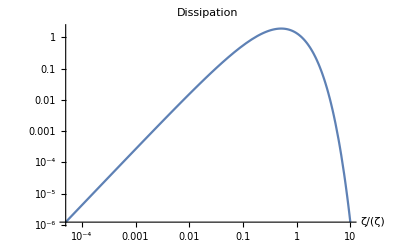

```mathematica
LogLogPlot[zetaBar FF[x zetaBar],{x,0.00005,10},PlotLabel->"Dissipation",AxesLabel->{ζ/ζ̄ }]
```

```mathematica
(*pdfPoints=Import["/home/sasha/Downloads/pdf_points.tsv","TSV"];*)
```

```mathematica
sigma = NIntegrate[FF[z](z - zetaBar)^2,{z,0,Infinity}]/ NIntegrate[FF[z],{z,0,Infinity}]
```

11.7443

```mathematica
norm =NIntegrate[FF[z],{z,0,Infinity}]
```

2.41667

```mathematica
GG[y_] := Log[FF[zetaBar - y Sqrt[sigma]]/ norm]
```

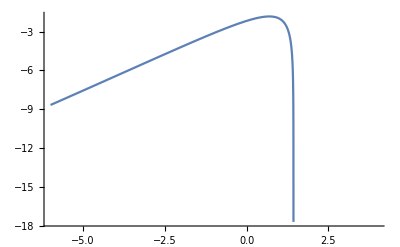

```mathematica
Plot[GG[y],{y,-6,4}]
```

```mathematica
Pμ[μ_,c_] :=-c/(1-μ)^2(c-a)(2 c +a)(2 a + c) E^(-(a^2 + c^2 + a c))/.a->c/(1-μ)//Simplify
```

```mathematica
Pμ[μ,c]
```

-(c^4 ⅇ^(-(c^2 (3-3 μ+μ^2))/(-1+μ)^2) (-3+μ) μ (-3+2 μ))/(-1+μ)^5

```mathematica
FullSimplify[(Pμ[μ,c] /D[c^(5/2),c] )/.c->(ζ/F[μ])^(2/5)]
```

-(2 ⅇ^(-((3+(-3+μ) μ) (ζ/F[μ])^(4/5))/(-1+μ)^2) ζ (-3+μ) μ (-3+2 μ))/(5 (-1+μ)^5 F[μ])